```mathematica
(*Function for finding the average of interpolating function for later: *)
FindAverage[fun_,a_,b_]:=(1/(b-a))*NIntegrate[fun,{t,a,b},WorkingPrecision->6, AccuracyGoal-> 8];
```

```mathematica
combineLists[list_]:=MapThread[Mean[{##}]&]/@GatherBy[list,Take[#,2]&]
```

```mathematica
payoffs={x*(γ* α−x),
x*( γ* (1-α^(1/c))^c −x),
x*(γ* αg−x),
γ*x*(1−α),
γ*x*(1−(1-α^(1/c))^c),
γ*x*(1−αg)};(*Payoffs for hosts (1 through 3)and symbionts (4 through 6)*)
```

Define Payoffs for type 1 and type 2 interactions:

```mathematica
{pi1match,pi1mismatch,pig,ψ1match,ψ1mismatch,ψg}=payoffs/.{α-> α1,γ-> γ1,x-> x1};
{pi2match,pi2mismatch,pigna,ψ2match,ψ2mismatch,ψgna}=payoffs/.{α-> α2,γ-> γ2,x-> x2};
(*Mutant Values*)
```

Frequency of Symbionts over time is given below:

```mathematica
S1 = v1*ψ1match+(1-v1)*ψ1mismatch; (*Symbiont 1 *)
S2 =  (1-v1)*ψ2match+v1*ψ2mismatch; (*Symbiont 2 *)
(*Symbiont Average Fitness: *)
Sbar = u1*S1+(1-u1)*S2 ;(*Average Symbiont Payoff*)
```

The system is reduced, i.e. the frequency of symbiont 2 is given as (1-u1) and the frequency of host 2 is given as (1-v1).

Host Average Payoffs:

```mathematica
H1=u1*pi1match +(1-u1)*pi2mismatch; (*Host 1 *)
H2 = u1*pi1mismatch+(1-u1)*pi2match;(*Host 2 *)

Hbar = v1*H1+(1-v1)*H2(*+(1-v1-v2)*HG*);(*Payoff received by a host on average*)
```

Expressions for the change in the frequency of the host and symbiont types over time:

```mathematica
(*Replicators: *)
S1D =Simplify[ u1 *(S1-Sbar)];
(*S2D =u2*(S2-Sbar);*)
V1=Simplify[v1(H1-Hbar)];(*Host 1*)
```

```mathematica
replicators={S1D,V1}/.{v1-> v1[t], u1-> u1[t]};
```

Format the system of ODE’s. In previous simulations I used 2 discrete variables whose value changed when a condition was satisfied, but in this simulation I won’t.

```mathematica
{u1'[t]==β[t]* replicators[[1]],v1'[t]==η[t]*replicators[[2]],u1[0]==u10,v1[0]==v10,β[0]==1,η[0]==1}
```

{u1'[t]==-(-1+u1[t]) u1[t] (x1 γ1 (1-(1-α1^(1/c))^c+(-α1+(1-α1^(1/c))^c) v1[t])+x2 γ2 (-1+α2-α2 v1[t]+(1-α2^(1/c))^c v1[t])) β[t],v1'[t]==(x2 (α2-(1-α2^(1/c))^c) γ2+x1 (-α1+(1-α1^(1/c))^c) γ1 u1[t]+x2 (-α2+(1-α2^(1/c))^c) γ2 u1[t]) (-1+v1[t]) v1[t] η[t],u1[0]==u10,v1[0]==v10,β[0]==1,η[0]==1}

Put it together in a System with no mutant symbionts (systemNMS). For now, I won’t use my conditional statements.

```mathematica
SystemNMS[α1_,α2_, c_,x1_,x2_,γ1_,γ2_,u10_,v10_]:={u1'[t]==-(-1+u1[t]) u1[t] (x1 γ1 (1-(1-α1^(1/c))^c+(-α1+(1-α1^(1/c))^c) v1[t])+x2 γ2 (-1+α2-α2 v1[t]+(1-α2^(1/c))^c v1[t])) β[t],v1'[t]==(x2 (α2-(1-α2^(1/c))^c) γ2+x1 (-α1+(1-α1^(1/c))^c) γ1 u1[t]+x2 (-α2+(1-α2^(1/c))^c) γ2 u1[t]) (-1+v1[t]) v1[t] η[t],u1[0]==u10,v1[0]==v10,β[0]==1,η[0]==1,

WhenEvent[v1'[t]==0,Sow[{t,v1[t]}], "DetectionMethod"-> "Interpolation","LocationMethod"->"LinearInterpolation"],
(*Set border conditions such that if the frequency of a host or symbiont becomes too high or low it returns to a value between 0 and 1. Allowing the frequency of a host or symbiont to reach 0 or 1 causes errors in later steps when finding the average value of later simulations. *)

WhenEvent [EvenQ[0]&&u1[t]<0.0001, u1[t]->0.0001 ,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&v1[t]<0.0001,v1[t]-> 0.0001,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1[t]>0.9999, u1[t]-> 0.9999,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&v1[t]>0.9999, v1[t]-> 0.9999,"LocationMethod"->"LinearInterpolation"]

(*
WhenEvent [EvenQ[0]&&u1[t]<0.0001, β[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0.0001,η[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1[t]>0.9999, β[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>0.9999, η[t]-> 0,"LocationMethod"->"LinearInterpolation"]*)

(*
WhenEvent [EvenQ[0]&&u1[t]<0.00001, u1[t]->0.00001 ,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&v1[t]<0.00001,v1[t]-> 0.00001,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1[t]>0.99999, u1[t]-> 0.99999,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&v1[t]>0.99999, v1[t]-> 0.99999,"LocationMethod"->"LinearInterpolation"]*)
(*
WhenEvent [EvenQ[0]&&u1[t]<0, u1[t]->0 ,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&v1[t]<0,v1[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1[t]>1, u1[t]-> 1,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&v1[t]>1, v1[t]-> 1,"LocationMethod"->"LinearInterpolation"]*)
}
```

Next I will define two new systems of ODEs. One will include a symbiont 1 mutant, and the other will include a symbiont 2 mutant. First will be the symbiont 1 mutant system. Here are the symbiont 1 payoffs:

```mathematica
{pi1MUmatch,pi1MUmismatch,pigna,ψ1MUmatch,ψ1MUmismatch,ψgna}=payoffs/.{α-> α1m,γ-> γ1m,x-> x1m};
```

Average payoff of symbionts phenotype:

```mathematica
S1 = v1*ψ1match+(1-v1)*ψ1mismatch;(*Symbiont 1*)
S2 =  v1*ψ2mismatch+(1-v1)*ψ2match;(*Symbiont 2*)
S1M =  v1*ψ1MUmatch +(1-v1)*ψ1MUmismatch;(*Symbiont 1 Mutant*)
SbarM1 =u1*S1+(1-u1-u1m)*S2+u1m*S1M; (*Payoff received for a symbiont picked at random*)
```

Average payoffs for host phenotypes:

```mathematica
H1m1=u1*pi1match +(1-u1-u1m)*pi2mismatch+u1m*pi1MUmatch;(*Host 1 *)
H2m1 = u1*pi1mismatch+(1-u1-u1m)*pi2match+u1m*pi1MUmismatch;(*Host 2 *)
HbarM1 =v1*H1m1+(1-v1)*H2m1(*Payoff received by a host on average*);
```

Frequencies:

```mathematica
S1D1 = u1(S1-SbarM1); (*Symbiont 1*)
SM11=u1m(S1M-SbarM1);(*Symbiont 1 mutant*)
V11=v1(H1m1-HbarM1);(*Host 1*)
```

```mathematica
replicators={S1D1,SM11, V11}/.{v1-> v1[t], u1-> u1[t],u1m-> u1m[t]};
```

Add discrete variables β, η, and μ to the system. The value of these variables will change from 1 to 0 when the frequency of a host or symbiont becomes sufficiently low. Thus the frequency will cease changing. This is for the purpose of reducing computational time required for the simulation.

```mathematica
ClearAll[v20,v10,c]
{u1'[t]==β[t]*replicators[[1]],u1m'[t]==μ[t]*replicators[[2]],v1'[t]==η[t]*replicators[[3]],u1[0]==u10,u1m[0]==u1m0,v1[0]==v10,β[0]==1,η[0]==1,μ[0]==1}
```

{u1'[t]==u1[t] (x1 (1-(1-α1^(1/c))^c) γ1 (1-v1[t])+x1 (1-α1) γ1 v1[t]-u1[t] (x1 (1-(1-α1^(1/c))^c) γ1 (1-v1[t])+x1 (1-α1) γ1 v1[t])-u1m[t] (x1m (1-(1-α1m^(1/c))^c) γ1m (1-v1[t])+x1m (1-α1m) γ1m v1[t])-(1-u1[t]-u1m[t]) (x2 (1-α2) γ2 (1-v1[t])+x2 (1-(1-α2^(1/c))^c) γ2 v1[t])) β[t],u1m'[t]==u1m[t] (x1m (1-(1-α1m^(1/c))^c) γ1m (1-v1[t])+x1m (1-α1m) γ1m v1[t]-u1[t] (x1 (1-(1-α1^(1/c))^c) γ1 (1-v1[t])+x1 (1-α1) γ1 v1[t])-u1m[t] (x1m (1-(1-α1m^(1/c))^c) γ1m (1-v1[t])+x1m (1-α1m) γ1m v1[t])-(1-u1[t]-u1m[t]) (x2 (1-α2) γ2 (1-v1[t])+x2 (1-(1-α2^(1/c))^c) γ2 v1[t])) μ[t],v1'[t]==v1[t] (x1 (-x1+α1 γ1) u1[t]+x2 (-x2+(1-α2^(1/c))^c γ2) (1-u1[t]-u1m[t])+x1m (-x1m+α1m γ1m) u1m[t]-(x1 (-x1+(1-α1^(1/c))^c γ1) u1[t]+x2 (-x2+α2 γ2) (1-u1[t]-u1m[t])+x1m (-x1m+(1-α1m^(1/c))^c γ1m) u1m[t]) (1-v1[t])-(x1 (-x1+α1 γ1) u1[t]+x2 (-x2+(1-α2^(1/c))^c γ2) (1-u1[t]-u1m[t])+x1m (-x1m+α1m γ1m) u1m[t]) v1[t]) η[t],u1[0]==u10,u1m[0]==u1m0,v1[0]==v10,β[0]==1,η[0]==1,μ[0]==1}

System with an invading symbiont 1 (SystemINV1S)

```mathematica
SystemINVS1[α1_,α1m_,α2_,c_,x1_,x1m_,x2_,γ1_,γ1m_,γ2_,u10_,u1m0_,v10_]:={u1'[t]==u1[t] (x1 (1-(1-α1^(1/c))^c) γ1 (1-v1[t])+x1 (1-α1) γ1 v1[t]-u1[t] (x1 (1-(1-α1^(1/c))^c) γ1 (1-v1[t])+x1 (1-α1) γ1 v1[t])-u1m[t] (x1m (1-(1-α1m^(1/c))^c) γ1m (1-v1[t])+x1m (1-α1m) γ1m v1[t])-(1-u1[t]-u1m[t]) (x2 (1-α2) γ2 (1-v1[t])+x2 (1-(1-α2^(1/c))^c) γ2 v1[t])) β[t],u1m'[t]==u1m[t] (x1m (1-(1-α1m^(1/c))^c) γ1m (1-v1[t])+x1m (1-α1m) γ1m v1[t]-u1[t] (x1 (1-(1-α1^(1/c))^c) γ1 (1-v1[t])+x1 (1-α1) γ1 v1[t])-u1m[t] (x1m (1-(1-α1m^(1/c))^c) γ1m (1-v1[t])+x1m (1-α1m) γ1m v1[t])-(1-u1[t]-u1m[t]) (x2 (1-α2) γ2 (1-v1[t])+x2 (1-(1-α2^(1/c))^c) γ2 v1[t])) μ[t],v1'[t]==v1[t] (x1 (-x1+α1 γ1) u1[t]+x2 (-x2+(1-α2^(1/c))^c γ2) (1-u1[t]-u1m[t])+x1m (-x1m+α1m γ1m) u1m[t]-(x1 (-x1+(1-α1^(1/c))^c γ1) u1[t]+x2 (-x2+α2 γ2) (1-u1[t]-u1m[t])+x1m (-x1m+(1-α1m^(1/c))^c γ1m) u1m[t]) (1-v1[t])-(x1 (-x1+α1 γ1) u1[t]+x2 (-x2+(1-α2^(1/c))^c γ2) (1-u1[t]-u1m[t])+x1m (-x1m+α1m γ1m) u1m[t]) v1[t]) η[t],u1[0]==u10,u1m[0]==u1m0,v1[0]==v10,β[0]==1,η[0]==1,μ[0]==1,

WhenEvent [EvenQ[0]&&u1[t]<0.000001, β[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1m[t]<0.000001, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0.000001,η[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1[t]>0.999999, β[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1m[t]>0.999999, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>0.999999, η[t]-> 0,"LocationMethod"->"LinearInterpolation"]
(*
WhenEvent [EvenQ[0]&&u1[t]<0.0000, β[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1m[t]<0.0000, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0.0000,η[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1[t]>1.0000, β[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1m[t]>1.0000, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>1.0000, η[t]-> 0,"LocationMethod"->"LinearInterpolation"]*)

(*We will restrict the values of the frequencies of each strategist restricted to [0,1] using conditional statements. Note that these statements use greater precision than the initial boundary conditions. This is because mutant frequency will be 0.05*(frequency of type invaded). At minima this could result in an extremely low value.  *)
(*
WhenEvent [EvenQ[0]&&u1[t]<0.00001, u1[t]->0.00001 ,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1m[t]<0.00001, u1m[t]->0.00001 ,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0.00001,v1[t]-> 0.00001,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1[t]>0.99999, u1[t]-> 0.99999,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1m[t]>0.99999, u1m[t]-> 0.99999,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>0.99999, v1[t]-> 0.99999,"LocationMethod"->"LinearInterpolation"]*)
(*
WhenEvent [EvenQ[0]&&u1[t]<0, u1[t]->0 ,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1m[t]<0, u1m[t]->0 ,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0,v1[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1[t]>1, u1[t]->1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1m[t]>1, u1m[t]->1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>1, v1[t]-> 1,"LocationMethod"->"LinearInterpolation"]*)
}
```

Next, I define the system of equations with symbiont 2 mutants. Here are the symbiont 2 mutant payoffs:

```mathematica
{pi2MUmatch,pi2MUmismatch,pigna,ψ2MUmatch,ψ2MUmismatch,ψgna}=payoffs/.{α-> α2m,γ-> γ2m,x-> x2m};
```

Average payoffs for symbiont phenotypes:

```mathematica
S1m2 = (1-v2)*ψ1match+(v2)*ψ1mismatch; (*Symbiont 1 average payoff*)
S2m2 =  (1-v2)*ψ2mismatch+(v2)*ψ2match(*Symbiont 2 *);
S2Mm2 =  (1-v2)*ψ2MUmismatch +(v2)*ψ2MUmatch(*Symbiont 2 mutant *);
SbarM2 = (1-u2-u2m)*S1m2+u2*S2m2+u2m*S2Mm2(*Average Symbiont Payoff all symbionts*);
```

Average Payoffs for host phenotypes:

```mathematica
H1m2=(1-u2-u2m)*pi1match +u2*pi2mismatch+u2m*pi2MUmismatch;(*Host 1 *)
H2m2 = (1-u2-u2m)*pi1mismatch+u2*pi2match+u2m*pi2MUmatch;(*Host 2 *)
HbarM2 =(1-v2)*H1m2+(v2)*H2m2(*Payoff received by a host on average*);
```

Frequency of each phenotype over time:

```mathematica
S2D2 = u2(S2m2-SbarM2);
SM22=u2m(S2Mm2-SbarM2);
V22=v2(H2m2-HbarM2);(*Host 1*)
```

```mathematica
replicators={S2D2,SM22, V22}/.{v2-> v2[t],u2m-> u2m[t],u2-> u2[t]};
```

Once more employ discrete variables :

```mathematica
{u2'[t]== δ[t]*replicators[[1]],u2m'[t]==μ[t]*replicators[[2]],v2'[t]==η[t]*replicators[[3]],u2m[0]==u2m0,u2[0]==u20,v2[0]==v20,δ[0]==1,η[0]==1,μ[0]==1}
```

{u2'[t]==u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 (1-v2[t])+x2 (1-α2) γ2 v2[t]-(1-u2[t]-u2m[t]) (x1 (1-α1) γ1 (1-v2[t])+x1 (1-(1-α1^(1/c))^c) γ1 v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 (1-v2[t])+x2 (1-α2) γ2 v2[t])-u2m[t] (x2m (1-(1-α2m^(1/c))^c) γ2m (1-v2[t])+x2m (1-α2m) γ2m v2[t])) δ[t],u2m'[t]==u2m[t] (x2m (1-(1-α2m^(1/c))^c) γ2m (1-v2[t])+x2m (1-α2m) γ2m v2[t]-(1-u2[t]-u2m[t]) (x1 (1-α1) γ1 (1-v2[t])+x1 (1-(1-α1^(1/c))^c) γ1 v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 (1-v2[t])+x2 (1-α2) γ2 v2[t])-u2m[t] (x2m (1-(1-α2m^(1/c))^c) γ2m (1-v2[t])+x2m (1-α2m) γ2m v2[t])) μ[t],v2'[t]==v2[t] (x2 (-x2+α2 γ2) u2[t]+x1 (-x1+(1-α1^(1/c))^c γ1) (1-u2[t]-u2m[t])+x2m (-x2m+α2m γ2m) u2m[t]-(x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]+x1 (-x1+α1 γ1) (1-u2[t]-u2m[t])+x2m (-x2m+(1-α2m^(1/c))^c γ2m) u2m[t]) (1-v2[t])-(x2 (-x2+α2 γ2) u2[t]+x1 (-x1+(1-α1^(1/c))^c γ1) (1-u2[t]-u2m[t])+x2m (-x2m+α2m γ2m) u2m[t]) v2[t]) η[t],u2m[0]==u2m0,u2[0]==u20,v2[0]==v20,δ[0]==1,η[0]==1,μ[0]==1}

System with an invading symbiont 2 (System INVS2)

```mathematica
SystemINVS2[α1_,α2m_,α2_,c_,x1_,x2m_,x2_,γ1_,γ2m_,γ2_,u20_,u2m0_,v20_]:={u2'[t]==u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 (1-v2[t])+x2 (1-α2) γ2 v2[t]-(1-u2[t]-u2m[t]) (x1 (1-α1) γ1 (1-v2[t])+x1 (1-(1-α1^(1/c))^c) γ1 v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 (1-v2[t])+x2 (1-α2) γ2 v2[t])-u2m[t] (x2m (1-(1-α2m^(1/c))^c) γ2m (1-v2[t])+x2m (1-α2m) γ2m v2[t])) δ[t],u2m'[t]==u2m[t] (x2m (1-(1-α2m^(1/c))^c) γ2m (1-v2[t])+x2m (1-α2m) γ2m v2[t]-(1-u2[t]-u2m[t]) (x1 (1-α1) γ1 (1-v2[t])+x1 (1-(1-α1^(1/c))^c) γ1 v2[t])-u2[t] (x2 (1-(1-α2^(1/c))^c) γ2 (1-v2[t])+x2 (1-α2) γ2 v2[t])-u2m[t] (x2m (1-(1-α2m^(1/c))^c) γ2m (1-v2[t])+x2m (1-α2m) γ2m v2[t])) μ[t],v2'[t]==v2[t] (x2 (-x2+α2 γ2) u2[t]+x1 (-x1+(1-α1^(1/c))^c γ1) (1-u2[t]-u2m[t])+x2m (-x2m+α2m γ2m) u2m[t]-(x2 (-x2+(1-α2^(1/c))^c γ2) u2[t]+x1 (-x1+α1 γ1) (1-u2[t]-u2m[t])+x2m (-x2m+(1-α2m^(1/c))^c γ2m) u2m[t]) (1-v2[t])-(x2 (-x2+α2 γ2) u2[t]+x1 (-x1+(1-α1^(1/c))^c γ1) (1-u2[t]-u2m[t])+x2m (-x2m+α2m γ2m) u2m[t]) v2[t]) η[t],u2m[0]==u2m0,u2[0]==u20,v2[0]==v20,δ[0]==1,η[0]==1,μ[0]==1,

WhenEvent [EvenQ[0]&&u2[t]<0.000001,δ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2m[t]<0.000001, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]<0.000001,η[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]>0.999999, δ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2m[t]>0.999999, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]>0.999999, η[t]-> 0,"LocationMethod"->"LinearInterpolation"]
(*
WhenEvent [EvenQ[0]&&u2[t]<0.0000,δ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2m[t]<0.0000, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]<0.0000,η[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]>1.0000, δ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2m[t]>1.0000, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]>1.0000, η[t]-> 0,"LocationMethod"->"LinearInterpolation"]*)
(*
WhenEvent [EvenQ[0]&&u2[t]<0.00001, u2[t]->0.00001 ,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2m[t]<0.00001, u2m[t]->0.00001 ,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]<0.00001,v2[t]-> 0.00001,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]>0.99999, u2[t]-> 0.99999,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2m[t]>0.99999, u2m[t]-> 0.99999,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]>0.99999, v2[t]-> 0.99999,"LocationMethod"->"LinearInterpolation"]*)(*WhenEvent [EvenQ[0]&&u2[t]<0, u2[t]->0 ,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2m[t]<0, u2m[t]->0 ,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]<0,v2[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]>1, u2[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2m[t]>1, u2m[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]>1, v2[t]-> 1,"LocationMethod"->"LinearInterpolation"]*)

}
```

```mathematica
(********************** A slightly lower version of ar2 *********************)

SymbiontInvFN[lar1_,har1_,lar2_,har2_,c1_,p_,d1_,u10_,v10_,a_]:=
(*The combine list function is used to take the average of sublists in a nested list whose first two elements match. For example my data structure is {{A, B, C, D},{A,B,E,F}, {G, H, I, J}} the function returns: 
{{A, B, Mean[C, E], Mean[D,F]}, {G, H, I, J}}. This will be helpful for averaging mutuant success across a variety initial starting frequencies. *)

combineLists[
Partition[(*<- Regroup table results*)
Flatten[(*<- Remove internal structure*)
ParallelTable[{Off[MapThread::mptd]; (*<- FindAverage sometimes returns a MapThread error when an interpolating function that lacks a necessary dimension is passed to it. I think occurs when the interpolating function value is constant for an entire sampled region. This is to be expected when a strategist goes extinct so I've turned this error off. *)

(*Run the system of equations, note that I can modulate the shape of the trade-off using the parameter C1, and can vary the initial conditions using the u10 and v10 terms.  *)
solution=Reap[NDSolve[ SystemNMS[ar1,ar2, c1,0.5,0.5,1,1,u10,v10],{u1, v1}, {t,0,10000},Method ->Automatic, MaxSteps->20^7,DiscreteVariables->{β,η},PrecisionGoal->a, AccuracyGoal-> a]];

sol=solution[[1,1]];
(*Estimate the period of the cycle resident population, and store that period as T1: *)

times=Flatten[solution[[2]],1][[All,1]];
(*timesa = minima or maxima of the cycle of host 1*)
values=Flatten[solution[[2]],1][[All,2]];
(*values = freauency of host a reaped at a mimimum or maximum. *)

(*Test to see if the system cycles. If it does not, assign an arbitrary period to it. *)
If[ Length[times]<4, TF=400, TF=2*Median[Differences[Drop[Flatten[times],1]]] ];

(*If the population fails to cycle we designate an arbitrary period of 400 (which is different from any of the "natural" periods for our parameters). Else, we find the differences between extrema to determine the period.  *)


{utest,v1test}= {u1[9999],v1[9999]}  /.Flatten[sol];

Which[ (*Test 1*) TF==400 &&utest>0.5, 
(*Simulation for a system without cycling, and a fixed host and symbiont 1: *)
(*Value 1*) {ar1,ar2,TF,
(*Initial conditions: *)
{u1f,v1f}={1,If[v1test>0.5,1,0]} ;
(*Because there are some cases where host 2 fixes we also test for this case above.*)				   
m11=Abs[0.05*u1f];
(*Subtract the frequency of the mutant from the frequency of the resident. *)
u1fm=Abs[u1f-m11];

(*************************** A slightly lower ar1: **************************)
am1=ar1-d1;
(*The mutant has a slightly lower ar1*)
sol4=NDSolve[SystemINVS1[ar1(*a match*), am1 (*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x1*),0.5(*x1m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u1fm(*u10*),m11(*u1m0*),v1f(*v1final*)], {u1,u1m,v1},{t,0,6*TF},DiscreteVariables->{β,μ,η}, MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];
(*Test to see if the mutant invades after invasion by comparing to its initial frequency: *)

{u1ans,m1ans,v1ans}= {u1[t],u1m[t],v1[t]}  /.Flatten[sol4];

avg1a=FindAverage[m1ans, 0,3*TF];
avg1b=FindAverage[m1ans, 3*TF,6*TF];
(*Mutants with greater fitness will increase from their intial average frequency. This was a critical change for creating plots that made sense. Word doc from email will explain. *)
sl1=If[avg1b>avg1a, 1,0],

(***************A slightly higher version of ar1: ****************)
am2=ar1+d1;

sol5=NDSolve[SystemINVS1[ar1(*a match*), am2 (*am match*),ar2(*a2*),(*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1fm(*u10*),m11(*v1f*),v1f(*u1m0*)], {u1,u1m,v1},{t,0,6*TF}, MaxSteps->20^7,DiscreteVariables->{β,μ,η},PrecisionGoal->a, AccuracyGoal-> a];


{u1ans,m1ans,v1ans}= {u1[t],u1m[t],v1[t]}  /.Flatten[sol5];

avg2a=FindAverage[m1ans, 0,3*TF];
avg2b=FindAverage[m1ans, 3*TF,6*TF];

sh1=If[avg2b>avg2a, 1,0],
(sh1-sl1),(*This is the vector for the ar1 component in the final plot. *)

(*ar2 does not evolve because symbiont 2 is extinct. *)
(*************** A slightly lower version of ar2 *********************)
(*Symbiont 2 does not evolve because it is extinct. *)
0,


(****************A slightly higher version of ar2 ****************)
0,
(****************Difference between values ****************)
0(*Vector for the ar2 component. *)
},


 (*Test 2 *)TF==400 &&utest<0.5,(*Value 2: *)
(*Symbiont 2 fixes and host 2 fixes.  *)


{  ar1,ar2,TF,
{u2f,v2f}={1,If[v1test<0.5,1,0]};

(*Mutants invade with a frequency that is proportional to the frequency of the type they invade: *)		   
m21=Abs[0.05*u2f];
(*Subtract the frequency of the mutant from the frequency of the resident. *)
u2fm=Abs[u2f-m21];


(*************************** A slightly lower ar1: **************************)
(*Symbiont 1 is extinct and does not mutate. *)
0,

(***************A slightly higher version of ar1: ****************)

0,
(***************Difference between values ****************)
0,
(********************** A slightly lower version of ar2 *********************)

am1=ar2-d1;

sol4=NDSolve[SystemINVS2[ar1(*a match*), am1(*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u2fm,m21(*uf0*),v2f(*v20*)], {u2,u2m,v2},{t,0,6*TF}, DiscreteVariables->{δ,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];

{u2ans,m2ans,v2ans}= {u2[t],u2m[t],v2[t]}  /.Flatten[sol4];


avg1a=FindAverage[m2ans, 0,3*TF];
avg1b=FindAverage[m2ans, 3*TF,6*TF];

sl2=If[avg1b>avg1a, 1,0],

(****************A slightly higher version of ar2 ****************)
am2=ar2+d1;

sol5=NDSolve[SystemINVS2[ar1(*a match*), am2 (*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u2fm,m21(*uf0*),v2f(*v20*)], {u2,u2m,v2},{t,0,6*TF}, DiscreteVariables->{δ,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];

{u2ans,m2ans,v2ans}= {u2[t],u2m[t],v2[t]} /.Flatten[sol5];

avg2a=FindAverage[m2ans, 0,3*TF];
avg2b=FindAverage[m2ans, 3*TF,6*TF];

sh2=If[avg2b>avg2a, 1,0],
(sh2-sl2)
},

(*Test 3*)TF ≠400,Table[{(*Value 3*)
ar1,ar2,TF,
(************************* initial conditions ***************************) 
{u1f,v1f}={u1[st],v1[st]}/.Flatten[sol]; 

 u2f=(1-u1f);
v2f=(1-v1f);               
(*Initial frequencies*)		   
m11=0.05*u1f;
m21=0.05*u2f;

u1fm=u1f-m11;
u2fm=u2f-m21;

(********************** A slightly lower ar1: ***************************)
am1=ar1-d1;
sol5=NDSolve[SystemINVS1[ar1(*a match*), am1(*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1fm,m11(*uf0*),v1f(*v20*)], {u1,u1m,v1},{t,0,12*TF}, Method -> Automatic, DiscreteVariables->{β,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];

{u1ans,m1ans1,v1ans}= {u1[t],u1m[t],v1[t]}  /.Flatten[sol5];


avg1a=FindAverage[m1ans1, 0,6*TF];
avg1b=FindAverage[m1ans1, 6*TF,12*TF];

s1=If[avg1b>avg1a, 1,0],

(************** A slightly higher version of ar1 *********************)
am2=ar1+d1;
sol6=NDSolve[SystemINVS1[ar1(*a match*), am2(*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1fm,m11(*uf0*),v1f(*v20*)], {u1,u1m,v1},{t,0,12*TF}, Method -> Automatic, DiscreteVariables->{β,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];
{u1ans,m1ans2,v1ans}= {u1[t],u1m[t],v1[t]}  /.Flatten[sol6];


avg2a=FindAverage[m1ans2,0,6*TF];
avg2b=FindAverage[m1ans2, 6*TF,12*TF];

s2=If[avg2b>avg2a, 1,0],
(s2-s1),
(************** A slightly lower version of ar2 *********************)
am3=ar2-d1;

sol6=NDSolve[SystemINVS2[ar1(*a match*), am3(*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u2fm,m21(*uf0*),v2f(*v20*)], {u2,u2m,v2},{t,0,12*TF},Method -> Automatic, DiscreteVariables->{δ,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];

{u2ans,m2ans1,v2ans}= {u2[t],u2m[t],v2[t]} /.Flatten[sol6];

avg3a=FindAverage[m2ans1, 0,6*TF];
avg3b=FindAverage[m2ans1, 6*TF,12*TF];

s3=If[avg3b>avg3a, 1,0],



(****************A slightly higher version of ar2 ****************)
am4=ar2+d1;

sol7=NDSolve[SystemINVS2[ar1(*a match*), am4 (*am match*),ar2(*a2*),(*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u2fm,m21(*uf0*),v2f(*v20*)], {u2,u2m,v2},{t,0,12*TF}, Method -> Automatic, DiscreteVariables->{δ,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];

{u2ans,m2ans2,v2ans}= {u2[t],u2m[t],v2[t]} /.Flatten[sol7];

avg4a=FindAverage[m2ans2,0,6*TF];
avg4b=FindAverage[m2ans2, 6*TF,12*TF];

s4=If[avg4b>avg4a, 1,0],
(s4-s3)},{st,3000+(p*TF),3000+TF,p*TF}](*<- closing bracket for table*)
](*<- closing bracket for Which Function*)





},{ar1,lar1,har1,0.01},{ar2,lar2,har2,0.01}](*<- Closing bracket for Parallel Table*)],9](*<- Closing bracket for Partition*)](*<- Closing bracket for CombineLists*)
```

```mathematica
icv1=SymbiontInvFN[0.55,0.85,0.55,0.85,1/2,0.1,0.005,0.66,0.34,6];
```

```mathematica
(*Export["icv1csymbionts.mat",icv1];*)
```

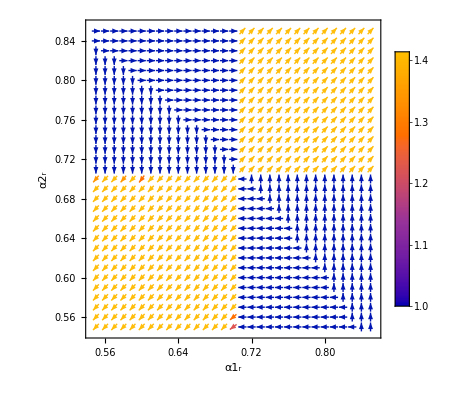

```mathematica
ListVectorPlot[Partition[Partition[Flatten[icv1[[All,{1,2,6,9}]]],2],2], FrameLabel-> {"α1_r","α2_r"}, PlotLegends->Automatic, VectorPoints -> All]
```

```mathematica
icv2=SymbiontInvFN[0.55,0.85,0.55,0.85,1/2,0.1,0.005,0.34,0.66,6];
```

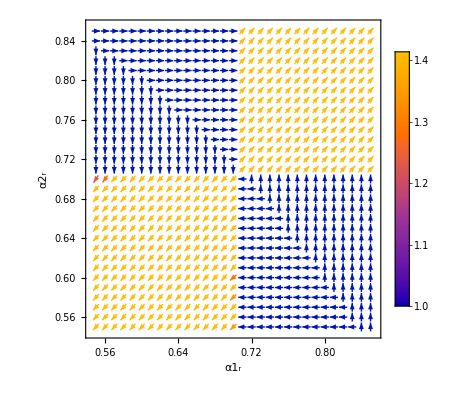

```mathematica
ListVectorPlot[Partition[Partition[Flatten[icv2[[All,{1,2,6,9}]]],2],2], FrameLabel-> {"α1_r","α2_r"}, PlotLegends->Automatic, VectorPoints -> All]
```

Combine the two plots to generate a symmetrical master plot:

```mathematica
combined=combineLists[Flatten[{Join[icv1,icv2]},1]];
```

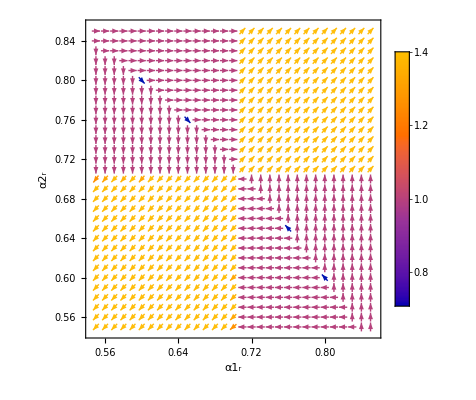

```mathematica
ListVectorPlot[Partition[Partition[Flatten[combined[[All,{1,2,6,9}]]],2],2], FrameLabel-> {"α1_r","α2_r"}, PlotLegends->Automatic, VectorPoints -> All]
```

```mathematica
(*Export["icv2csymbionts.mat",icv2];*)
```

Now we’ll repeat this process for invading host mutants

Now h1, h2, mh1, and mh2 each need their own payoffs:

```mathematica
{pi1match,pi1mismatch,pig,ψ1match,ψ1mismatch,ψg}=payoffs/.{α-> α1,γ-> γ1,x-> x1};
{pi2match,pi2mismatch,pigna,ψ2match,ψ2mismatch,ψgna}=payoffs/.{α-> α2,γ-> γ2,x-> x2};
{pi1MUmatch,pi1MUmismatch,pigna,ψ1MUmatch,ψ1MUmismatch,ψgna}=payoffs/.{α-> α1m,γ-> γ1m,x-> x1m};
{pi2MUmatch,pi2MUmismatch,pigna,ψ2MUmatch,ψ2MUmismatch,ψgna}=payoffs/.{α-> α2m,γ-> γ2m,x-> x2m};
```

Now expressions for the fitness when there are h1 mutants:

```mathematica
S1 = v1*ψ1match+(1-v1)*ψ2mismatch;
S2 =  v1*ψ1mismatch+(1-v1)*ψ2match;
Sbar =u1*S1+(1-u1)*S2;
```

```mathematica
H1=u1*pi1match +(1-u1)*pi1mismatch;(*Host 1 *)
H2 = u1*pi2mismatch+(1-u1)*pi2match;(*Host 2 *)
Hbar =v1*H1+(1-v1)*H2;(*Payoff received by a host on average*)
```

```mathematica
U1 = u1(S1-Sbar);
V1=v1(H1-Hbar);(*Host 1*)
```

```mathematica
replicators={U1,V1}/.{v1-> v1[t], u1-> u1[t]};
```

```mathematica
{u1'[t]==β[t]*replicators[[1]],v1'[t]==η[t]*replicators[[2]],u1[0]==u10,v1[0]==v10,β[0]==1,η[0]==1}
```

{u1'[t]==u1[t] (x2 (1-(1-α2^(1/c))^c) γ2 (1-v1[t])+x1 (1-α1) γ1 v1[t]-u1[t] (x2 (1-(1-α2^(1/c))^c) γ2 (1-v1[t])+x1 (1-α1) γ1 v1[t])-(1-u1[t]) (x2 (1-α2) γ2 (1-v1[t])+x1 (1-(1-α1^(1/c))^c) γ1 v1[t])) β[t],v1'[t]==v1[t] (x1 (-x1+(1-α1^(1/c))^c γ1) (1-u1[t])+x1 (-x1+α1 γ1) u1[t]-(x2 (-x2+α2 γ2) (1-u1[t])+x2 (-x2+(1-α2^(1/c))^c γ2) u1[t]) (1-v1[t])-(x1 (-x1+(1-α1^(1/c))^c γ1) (1-u1[t])+x1 (-x1+α1 γ1) u1[t]) v1[t]) η[t],u1[0]==u10,v1[0]==v10,β[0]==1,η[0]==1}

```mathematica
(*System of equations with no mutant hosts:  *)
SystemNMH[α1_,α2_, c_,x1_,x2_,γ1_,γ2_,u10_,v10_]:={u1'[t]==u1[t] (x2 (1-(1-α2^(1/c))^c) γ2 (1-v1[t])+x1 (1-α1) γ1 v1[t]-u1[t] (x2 (1-(1-α2^(1/c))^c) γ2 (1-v1[t])+x1 (1-α1) γ1 v1[t])-(1-u1[t]) (x2 (1-α2) γ2 (1-v1[t])+x1 (1-(1-α1^(1/c))^c) γ1 v1[t])) β[t],v1'[t]==v1[t] (x1 (-x1+(1-α1^(1/c))^c γ1) (1-u1[t])+x1 (-x1+α1 γ1) u1[t]-(x2 (-x2+α2 γ2) (1-u1[t])+x2 (-x2+(1-α2^(1/c))^c γ2) u1[t]) (1-v1[t])-(x1 (-x1+(1-α1^(1/c))^c γ1) (1-u1[t])+x1 (-x1+α1 γ1) u1[t]) v1[t]) η[t],u1[0]==u10,v1[0]==v10,β[0]==1,η[0]==1,
(*Conditional statements that stores when extrema occur. This will be necessary to find the period of cycles later: *)

WhenEvent[u1'[t]==0,Sow[{t,u1[t]}], "DetectionMethod"-> "Interpolation","LocationMethod"->"LinearInterpolation"],

(*We will restrict the values of the frequencies of each strategist restricted to [0,1] using conditional statements: *)
(*
WhenEvent [EvenQ[0]&&u1[t]<0.001, β[t]-> 0,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&v1[t]<0.001,η[t]-> 0,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&u1[t]>0.999, β[t]-> 0,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&v1[t]>0.999, η[t]-> 0,"LocationMethod"->"LinearInterpolation"]
*)

WhenEvent [EvenQ[0]&&u1[t]<0.0001,u1[t]-> 0.0001,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&v1[t]<0.0001,v1[t]-> 0.0001,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&u1[t]>0.9999, u1[t]-> 0.9999,"LocationMethod"->"LinearInterpolation"],

WhenEvent [EvenQ[0]&&v1[t]>0.9999,v1[t]-> 0.9999,"LocationMethod"->"LinearInterpolation"]
}
```

Now for a system with a mutant host 1:

```mathematica
(**************************** Host 1 Mutant: ***********************************)
```

```mathematica
S1 = v1*ψ1match+(1-v1-v1m)*ψ2mismatch+v1m*ψ1MUmatch;
S2 =  v1*ψ1mismatch+(1-v1-v1m)*ψ2match+v1m*ψ1MUmismatch;
SbarM1 =u1*S1+(1-u1)*S2;
```

```mathematica
H1=u1*pi1match +(1-u1)*pi1mismatch;(*Host 1 *)
H1m=u1*pi1MUmatch +(1-u1)*pi1MUmismatch;(*Host 1 *)
H2 = u1*pi2mismatch+(1-u1)*pi2match;(*Host 2 *)
HbarM1 =v1*H1+(1-v1-v1m)*H2+v1m*H1m;(*Payoff received by a host on average*)
```

```mathematica
U1 = u1(S1-SbarM1);
V1=v1(H1-HbarM1);(*Host 1*)
V1M=v1m(H1m-HbarM1);
```

```mathematica
replicators={U1, V1,V1M}/.{v1-> v1[t], u1-> u1[t],v1m-> v1m[t]};
```

```mathematica
ClearAll[v20,v10,c]
{u1'[t]==β[t]*replicators[[1]],v1'[t]==η[t]*replicators[[2]],v1m'[t]==μ[t]*replicators[[3]],u1[0]==u10,v1m[0]==v1m0,v1[0]==v10,β[0]==1,η[0]==1,μ[0]==1}
```

{u1'[t]==u1[t] (x1 (1-α1) γ1 v1[t]+x2 (1-(1-α2^(1/c))^c) γ2 (1-v1[t]-v1m[t])+x1m (1-α1m) γ1m v1m[t]-u1[t] (x1 (1-α1) γ1 v1[t]+x2 (1-(1-α2^(1/c))^c) γ2 (1-v1[t]-v1m[t])+x1m (1-α1m) γ1m v1m[t])-(1-u1[t]) (x1 (1-(1-α1^(1/c))^c) γ1 v1[t]+x2 (1-α2) γ2 (1-v1[t]-v1m[t])+x1m (1-(1-α1m^(1/c))^c) γ1m v1m[t])) β[t],v1'[t]==v1[t] (x1 (-x1+(1-α1^(1/c))^c γ1) (1-u1[t])+x1 (-x1+α1 γ1) u1[t]-(x1 (-x1+(1-α1^(1/c))^c γ1) (1-u1[t])+x1 (-x1+α1 γ1) u1[t]) v1[t]-(x2 (-x2+α2 γ2) (1-u1[t])+x2 (-x2+(1-α2^(1/c))^c γ2) u1[t]) (1-v1[t]-v1m[t])-(x1m (-x1m+(1-α1m^(1/c))^c γ1m) (1-u1[t])+x1m (-x1m+α1m γ1m) u1[t]) v1m[t]) η[t],v1m'[t]==v1m[t] (x1m (-x1m+(1-α1m^(1/c))^c γ1m) (1-u1[t])+x1m (-x1m+α1m γ1m) u1[t]-(x1 (-x1+(1-α1^(1/c))^c γ1) (1-u1[t])+x1 (-x1+α1 γ1) u1[t]) v1[t]-(x2 (-x2+α2 γ2) (1-u1[t])+x2 (-x2+(1-α2^(1/c))^c γ2) u1[t]) (1-v1[t]-v1m[t])-(x1m (-x1m+(1-α1m^(1/c))^c γ1m) (1-u1[t])+x1m (-x1m+α1m γ1m) u1[t]) v1m[t]) μ[t],u1[0]==u10,v1m[0]==v1m0,v1[0]==v10,β[0]==1,η[0]==1,μ[0]==1}

```mathematica
SystemINVH1[α1_,α1m_,α2_,c_,x1_,x1m_,x2_,γ1_,γ1m_,γ2_,u10_,v10_,v1m0_]:={u1'[t]==u1[t] (x1 (1-α1) γ1 v1[t]+x2 (1-(1-α2^(1/c))^c) γ2 (1-v1[t]-v1m[t])+x1m (1-α1m) γ1m v1m[t]-u1[t] (x1 (1-α1) γ1 v1[t]+x2 (1-(1-α2^(1/c))^c) γ2 (1-v1[t]-v1m[t])+x1m (1-α1m) γ1m v1m[t])-(1-u1[t]) (x1 (1-(1-α1^(1/c))^c) γ1 v1[t]+x2 (1-α2) γ2 (1-v1[t]-v1m[t])+x1m (1-(1-α1m^(1/c))^c) γ1m v1m[t])) β[t],v1'[t]==v1[t] (x1 (-x1+(1-α1^(1/c))^c γ1) (1-u1[t])+x1 (-x1+α1 γ1) u1[t]-(x1 (-x1+(1-α1^(1/c))^c γ1) (1-u1[t])+x1 (-x1+α1 γ1) u1[t]) v1[t]-(x2 (-x2+α2 γ2) (1-u1[t])+x2 (-x2+(1-α2^(1/c))^c γ2) u1[t]) (1-v1[t]-v1m[t])-(x1m (-x1m+(1-α1m^(1/c))^c γ1m) (1-u1[t])+x1m (-x1m+α1m γ1m) u1[t]) v1m[t]) η[t],v1m'[t]==v1m[t] (x1m (-x1m+(1-α1m^(1/c))^c γ1m) (1-u1[t])+x1m (-x1m+α1m γ1m) u1[t]-(x1 (-x1+(1-α1^(1/c))^c γ1) (1-u1[t])+x1 (-x1+α1 γ1) u1[t]) v1[t]-(x2 (-x2+α2 γ2) (1-u1[t])+x2 (-x2+(1-α2^(1/c))^c γ2) u1[t]) (1-v1[t]-v1m[t])-(x1m (-x1m+(1-α1m^(1/c))^c γ1m) (1-u1[t])+x1m (-x1m+α1m γ1m) u1[t]) v1m[t]) μ[t],u1[0]==u10,v1m[0]==v1m0,v1[0]==v10,β[0]==1,η[0]==1,μ[0]==1,


(*We will restrict the values of the frequencies of each strategist restricted to [0,1] using conditional statements: *)
(*
WhenEvent [EvenQ[0]&&u1[t]<0.0001, u1[t]->0.0001 ,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1m[t]<0.0001, v1m[t]-> 0.0001,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0.0001,v1[t]-> 0.0001,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1[t]>0.9999, u1[t]-> 0.9999,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1m[t]>0.9999, v1m[t]-> 0.9999,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>0.9999, v1[t]-> 0.9999,"LocationMethod"->"LinearInterpolation"]*)

WhenEvent [EvenQ[0]&&u1[t]<0.000001, β[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1m[t]<0.000001, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0.000001,η[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u1[t]>0.999999, β[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1m[t]>0.999999, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>0.999999, η[t]-> 0,"LocationMethod"->"LinearInterpolation"]
}
```

```mathematica
(**************************** Symbiont 2 Mutant: ***********************************)
```

```mathematica
S1 = (1-v2-v2m)*ψ1match+v2*ψ2mismatch+v2m*ψ2MUmismatch;
S2 =  (1-v2-v2m)*ψ1mismatch+v2*ψ2match+v2m*ψ2MUmatch;
SbarM2 =(1-u2)*S1+u2*S2;
```

```mathematica
H1=(1-u2)*pi1match +u2*pi1mismatch;(*Host 1 *)
H2m=(1-u2)*pi2MUmismatch +u2*pi2MUmatch;(*Host 1 *)
H2 = (1-u2)*pi2mismatch+u2*pi2match;(*Host 2 *)
HbarM2 =(1-v2-v2m)*H1+v2*H2+v2m*H2m;(*Payoff received by a host on average*)
```

```mathematica
U2 = u2(S2-SbarM2);
V2=v2(H2-HbarM2);(*Host 1*)
V2M=v2m(H2m-HbarM2);
```

```mathematica
replicators={U2,V2, V2M}/.{v2-> v2[t],u2-> u2[t],v2m-> v2m[t]};
```

```mathematica
ClearAll[v20,v10,c]
{u2'[t]==δ[t]*replicators[[1]],v2'[t]==η[t]*replicators[[2]],v2m'[t]==μ[t]*replicators[[3]],u2[0]==u20,v2m[0]==v2m0,v2[0]==v20,δ[0]==1,μ[0]==1,η[0]==1}
```

{u2'[t]==u2[t] (x2 (1-α2) γ2 v2[t]+x1 (1-(1-α1^(1/c))^c) γ1 (1-v2[t]-v2m[t])+x2m (1-α2m) γ2m v2m[t]-u2[t] (x2 (1-α2) γ2 v2[t]+x1 (1-(1-α1^(1/c))^c) γ1 (1-v2[t]-v2m[t])+x2m (1-α2m) γ2m v2m[t])-(1-u2[t]) (x2 (1-(1-α2^(1/c))^c) γ2 v2[t]+x1 (1-α1) γ1 (1-v2[t]-v2m[t])+x2m (1-(1-α2m^(1/c))^c) γ2m v2m[t])) δ[t],v2'[t]==v2[t] (x2 (-x2+(1-α2^(1/c))^c γ2) (1-u2[t])+x2 (-x2+α2 γ2) u2[t]-(x2 (-x2+(1-α2^(1/c))^c γ2) (1-u2[t])+x2 (-x2+α2 γ2) u2[t]) v2[t]-(x1 (-x1+α1 γ1) (1-u2[t])+x1 (-x1+(1-α1^(1/c))^c γ1) u2[t]) (1-v2[t]-v2m[t])-(x2m (-x2m+(1-α2m^(1/c))^c γ2m) (1-u2[t])+x2m (-x2m+α2m γ2m) u2[t]) v2m[t]) η[t],v2m'[t]==v2m[t] (x2m (-x2m+(1-α2m^(1/c))^c γ2m) (1-u2[t])+x2m (-x2m+α2m γ2m) u2[t]-(x2 (-x2+(1-α2^(1/c))^c γ2) (1-u2[t])+x2 (-x2+α2 γ2) u2[t]) v2[t]-(x1 (-x1+α1 γ1) (1-u2[t])+x1 (-x1+(1-α1^(1/c))^c γ1) u2[t]) (1-v2[t]-v2m[t])-(x2m (-x2m+(1-α2m^(1/c))^c γ2m) (1-u2[t])+x2m (-x2m+α2m γ2m) u2[t]) v2m[t]) μ[t],u2[0]==u20,v2m[0]==v2m0,v2[0]==v20,δ[0]==1,μ[0]==1,η[0]==1}

```mathematica
SystemINVH2[α1_,α2m_,α2_,c_,x1_,x2m_,x2_,γ1_,γ2m_,γ2_,u20_,v2m0_,v20_]:={u2'[t]==u2[t] (x2 (1-α2) γ2 v2[t]+x1 (1-(1-α1^(1/c))^c) γ1 (1-v2[t]-v2m[t])+x2m (1-α2m) γ2m v2m[t]-u2[t] (x2 (1-α2) γ2 v2[t]+x1 (1-(1-α1^(1/c))^c) γ1 (1-v2[t]-v2m[t])+x2m (1-α2m) γ2m v2m[t])-(1-u2[t]) (x2 (1-(1-α2^(1/c))^c) γ2 v2[t]+x1 (1-α1) γ1 (1-v2[t]-v2m[t])+x2m (1-(1-α2m^(1/c))^c) γ2m v2m[t])) δ[t],v2'[t]==v2[t] (x2 (-x2+(1-α2^(1/c))^c γ2) (1-u2[t])+x2 (-x2+α2 γ2) u2[t]-(x2 (-x2+(1-α2^(1/c))^c γ2) (1-u2[t])+x2 (-x2+α2 γ2) u2[t]) v2[t]-(x1 (-x1+α1 γ1) (1-u2[t])+x1 (-x1+(1-α1^(1/c))^c γ1) u2[t]) (1-v2[t]-v2m[t])-(x2m (-x2m+(1-α2m^(1/c))^c γ2m) (1-u2[t])+x2m (-x2m+α2m γ2m) u2[t]) v2m[t]) η[t],v2m'[t]==v2m[t] (x2m (-x2m+(1-α2m^(1/c))^c γ2m) (1-u2[t])+x2m (-x2m+α2m γ2m) u2[t]-(x2 (-x2+(1-α2^(1/c))^c γ2) (1-u2[t])+x2 (-x2+α2 γ2) u2[t]) v2[t]-(x1 (-x1+α1 γ1) (1-u2[t])+x1 (-x1+(1-α1^(1/c))^c γ1) u2[t]) (1-v2[t]-v2m[t])-(x2m (-x2m+(1-α2m^(1/c))^c γ2m) (1-u2[t])+x2m (-x2m+α2m γ2m) u2[t]) v2m[t]) μ[t],u2[0]==u20,v2m[0]==v2m0,v2[0]==v20,δ[0]==1,μ[0]==1,η[0]==1,

(*We will restrict the values of the frequencies of each strategist restricted to [0,1] using conditional statements: *)


(*
WhenEvent [EvenQ[0]&&v2m[t]<0.0001, v2m[t]-> 0.0001,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]<0.0001,u2[t]-> 0.0001,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]<0.0001,v2[t]-> 0.0001,"LocationMethod"->"LinearInterpolation"],


WhenEvent [EvenQ[0]&&v2m[t]>1, v2m[t]-> 0.9999,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]>1,u2[t]-> 0.9999,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]>1, v2[t]-> 0.9999,"LocationMethod"->"LinearInterpolation"]*)

WhenEvent [EvenQ[0]&&u2[t]<0.000001,δ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2m[t]<0.000001, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]<0.000001,η[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&u2[t]>0.999999, δ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2m[t]>0.999999, μ[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v2[t]>0.999999, η[t]-> 0,"LocationMethod"->"LinearInterpolation"]

}
```

```mathematica
(********************** A slightly lower version of ar2 *********************)

CleanFNH[lar1_,har1_,lar2_,har2_,c1_,p_,d1_,u00_,v100_]:=
combineLists[
Partition[Flatten[
ParallelTable[{Off[MapThread::mptd]; 
solution=Reap[NDSolve[ SystemNMH[ar1,ar2, c1,0.5,0.5,1,1,u00,v100],{u1, v1}, {t,0,10000},Method ->Automatic, MaxSteps->20^7,DiscreteVariables->{β,η}]];

sol=solution[[1,1]];
(*Estimate the period of the cycle resident population, and store that period as T1: *)

timesa=Flatten[solution[[2]],1][[All,1]];
(*timesa = minima or maxima of the cycle of host 1*)
values=Flatten[solution[[2]],1][[All,2]];
(*values = freauency of host a reaped at a mimimum or maximum. *)

(*Test to see if the system cycles. If it does not, assign an arbitrary period to it. *)
If[ Length[timesa]<4, times ={1000,1200,1400,1600,1800,2000}, times=timesa ];


TF=2*Median[Differences[Drop[Flatten[times],1]]];


{u1test,v1test}= {u1[10000],v1[10000]}  /.Flatten[sol];

Which[ (*Test 1*) TF==400 &&v1test>0.5, 
(*Simulation for a system without cycling, and a fixed host and symbiont 1: *)
(*Value 1*) {ar1,
ar2,
(*Initial conditions *)
u1f=If[u1test > 0.5,1,0];
v1f=1;
				   
m11=0.05*v1f;
(*Subtract the frequency of the mutant from the frequency of the resident. *)
v1fm=v1f-m11;

(*************************** A slightly lower ar1: **************************)
am1=ar1-d1;
(*The mutant has a slightly lower ar*)
(*SystemINVH1[α1_,α1m_,α2_,c_,x1_,x1m_,x2_,γ1_,γ1m_,γ2_,u10_,v10_,v1m0_]*)
sol4=NDSolve[SystemINVH1[ar1(*a match*), am1 (*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x1*),0.5(*x1m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u1f(*u10*),v1fm(*u1m0*),m11(*v1final*)], {u1,v1m,v1},{t,0,6*TF},DiscreteVariables->{β,μ,η}, MaxSteps->20^7];
(*Test to see if the mutant invades after invasion by comparing to its initial frequency: *)

{u1ans,m1ans,v1ans}= {u1[t],v1m[t],v1[t]}  /.Flatten[sol4];

avg1a=FindAverage[m1ans, 0,3*TF];
avg1b=FindAverage[m1ans, 3*TF,6*TF];

sh2=If[avg1b>avg1a, 1,0],

(***************A slightly higher version of ar1: ****************)
am2=ar1+d1;

sol5=NDSolve[SystemINVH1[ar1(*a match*), am2 (*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x1*),0.5(*x1m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u1f(*u10*),v1fm(*u1m0*),m11(*v1final*)], {u1,v1m,v1},{t,0,6*TF},DiscreteVariables->{β,μ,η}, MaxSteps->20^7];
(*Test to see if the mutant invades after invasion by comparing to its initial frequency: *)

{u1ans,m1ans,v1ans}= {u1[t],v1m[t],v1[t]}   /.Flatten[sol5];

avg2a=FindAverage[m1ans, 0,3*TF];
avg2b=FindAverage[m1ans, 3*TF,6*TF];

sh1=If[avg2b>avg2a, 1,0],
(sh1-sh2),

0,

0,0
},


 (*Test 3 *)TF==400 &&v1test<0.5,(*Value 2: *)
(*Symbiont 2 fixes and host 2 fixes.  *)


{ar1,
ar2,
{u2f,v2f}={If[u1test<0.5,1,0],1}  ;
  					   
m21=Abs[0.05*v2f];
(*Subtract the frequency of the mutant from the frequency of the resident. *)
v2fm=Abs[v2f-m21];


(*************************** A slightly lower ar1: **************************)
(*Symbiont 1 is extinct and does not mutate. *)
0,

(***************A slightly higher version of ar1: ****************)

0,
0,
(********************** A slightly lower version of ar2 *********************)

am1=ar2-d1;
(*SystemINVH2[α1_,α2m_,α2_,c_,x1_,x2m_,x2_,γ1_,γ2m_,γ2_,u20_,v2m0_,v20_]*)
sol4=NDSolve[SystemINVH2[ar1(*a match*), am1(*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u2f,m21(*v2m0*),v2fm(*v20*)], {u2,v2m,v2},{t,0,6*TF}, DiscreteVariables->{δ,μ,η},MaxSteps->20^7];

{u2ans,m2ans,v2ans}= {u2[t],v2m[t],v2[t]}  /.Flatten[sol4];


avg1a=FindAverage[m2ans, 0,3*TF];
avg1b=FindAverage[m2ans, 3*TF,6*TF];

sl1=If[avg1b>avg1a, 1,0],

(****************A slightly higher version of ar2 ****************)
am2=ar2+d1;

sol5=NDSolve[SystemINVH2[ar1(*a match*), am2 (*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u2f(*u20*),m21(*v2m0*),v2fm(*v20*)], {u2,v2m,v2},{t,0,6*TF}, DiscreteVariables->{δ,μ,η},MaxSteps->20^7];

{u2ans,m2ans,v2ans}= {u2[t],v2m[t],v2[t]} /.Flatten[sol5];

avg2a=FindAverage[m2ans, 0,3*TF];
avg2b=FindAverage[m2ans, 3*TF,6*TF];

sl2=If[avg2b>avg2a, 1,0],
(sl2-sl1)
},

(*Test 5*)TF ≠ 400,{Table[{(*Value 5*)
(*The system cycles, so we introduce mutants at every p *T of the resident cycle: *)





(**************************** initial conditions ***************************) 
{u1f,v1f}={u1[st],v1[st]}/.Flatten[sol]; 

 u2f=(1-u1f);
v2f=(1-v1f);               
(*Initial frequencies*)		   
m11=0.05*v1f;
m21=0.05*v2f;

v1fm=v1f-m11;
v2fm=v2f-m21;
ar1,
ar2,
(************************* A slightly lower ar1: ***************************)
am1=ar1-d1;
(*SystemINVH1[α1_,α1m_,α2_,c_,x1_,x1m_,x2_,γ1_,γ1m_,γ2_,u10_,v10_,v1m0_]*)
sol5=NDSolve[SystemINVH1[ar1(*a match*), am1(*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1f,v1fm(*v1f*),m11(*v1m0*)], {u1,v1m,v1},{t,0,15*TF}, Method -> Automatic, DiscreteVariables->{β,μ,η},MaxSteps->20^7];

{u1ans,m1ans1,v1ans}= {u1[t],v1m[t],v1[t]}  /.Flatten[sol5];


avg1a=FindAverage[m1ans1, 0*TF,6*TF];
avg1b=FindAverage[m1ans1, 6*TF,12*TF];

s1=If[avg1b>avg1a, 1,0],

(************** A slightly higher version of ar1 *********************)
am2=ar1+d1;
(*SystemINVH1[α1_,α1m_,α2_,c_,x1_,x1m_,x2_,γ1_,γ1m_,γ2_,u10_,v10_,v1m0_]*)
sol6=NDSolve[SystemINVH1[ar1(*a match*), am2(*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1f,v1fm(*v1f*),m11(*v1m0*)], {u1,v1m,v1},{t,0,15*TF}, Method -> Automatic, DiscreteVariables->{β,μ,η},MaxSteps->20^7];
{u1ans,m1ans2,v1ans}= {u1[t],v1m[t],v1[t]}  /.Flatten[sol6];


avg2a=FindAverage[m1ans2, 0*TF,6*TF];
avg2b=FindAverage[m1ans2, 6*TF,12*TF];

s2=If[avg2b>avg2a, 1,0],
(s2-s1),
(************** A slightly lower version of ar2 *********************)
am3=ar2-d1;
(*SystemINVH2[α1_,α2m_,α2_,c_,x1_,x2m_,x2_,γ1_,γ2m_,γ2_,u20_,v2m0_,v20_]*)
sol6=NDSolve[SystemINVH2[ar1(*a match*), am3(*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u2f,m21(*uf0*),v2fm(*v20*)], {u2,v2m,v2},{t,0,15*TF},Method -> Automatic, DiscreteVariables->{δ,μ,η},MaxSteps->20^7];

{u2ans,m2ans1,v2ans}= {u2[t],v2m[t],v2[t]} /.Flatten[sol6];

avg3a=FindAverage[m2ans1, 0,6*TF];
avg3b=FindAverage[m2ans1, 6*TF,12*TF];

s3=If[avg3b>avg3a, 1,0],



(****************A slightly higher version of ar2 ****************)
am4=ar2+d1;
(*SystemINVH2[α1_,α2m_,α2_,c_,x1_,x2m_,x2_,γ1_,γ2m_,γ2_,u20_,v2m0_,v20_]*)
sol7=NDSolve[SystemINVH2[ar1(*a match*), am4 (*am match*),ar2(*a2*),(*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u2f,m21(*uf0*),v2fm(*v20*)], {u2,v2m,v2},{t,0,15*TF}, Method -> Automatic, DiscreteVariables->{δ,μ,η},MaxSteps->20^7];

{u2ans,m2ans2,v2ans}= {u2[t],v2m[t],v2[t]} /.Flatten[sol7];

avg4a=FindAverage[m2ans2, 0,6*TF];
avg4b=FindAverage[m2ans2, 6*TF,12*TF];

s4=If[avg4b>avg4a, 1,0],

(s4-s3)



},{st,3000+(p*TF),3000+TF,p*TF}]}]},{ar1,lar1,har1,0.01},{ar2,lar2,har2,0.01}]],8]];
```

Run the simulation for one set of initial conditions:

```mathematica
problemzone2=CleanFNH[0.55,0.95,0.55,0.95,1/2,0.1,0.005,0.66,0.34];
```

```mathematica
(*Export[problemzone2.mat,problemzone2];*)
```

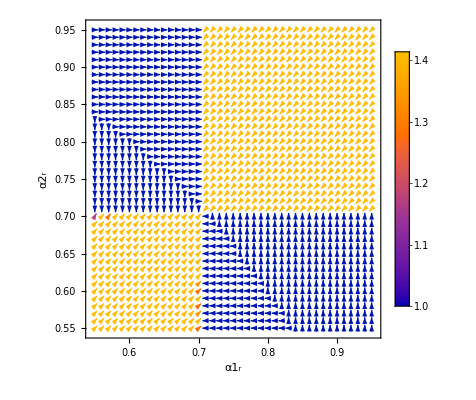

```mathematica
ListVectorPlot[Partition[Partition[Flatten[problemzone2[[All,{1,2,5,8}]]],2],2], FrameLabel-> {"α1_r","α2_r"}, PlotLegends->Automatic, VectorPoints -> All]
```

Consider the opposite set of initial conditions:

```mathematica
function2=CleanFNH[0.55,0.95,0.55,0.95,1/2,0.1,0.005,0.34,0.66];
```

```mathematica
(*Export[function2.mat,function2];*)
```

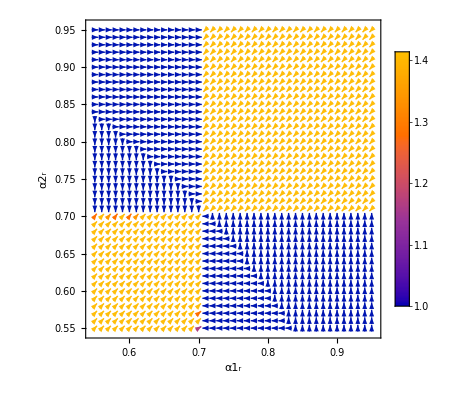

```mathematica
ListVectorPlot[Partition[Partition[Flatten[function2[[All,{1,2,5,8}]]],2],2], FrameLabel-> {"α1_r","α2_r"}, PlotLegends->Automatic, VectorPoints -> All]
```

```mathematica
combined2=combineLists[Flatten[{Join[problemzone2,function2]},1]];
```

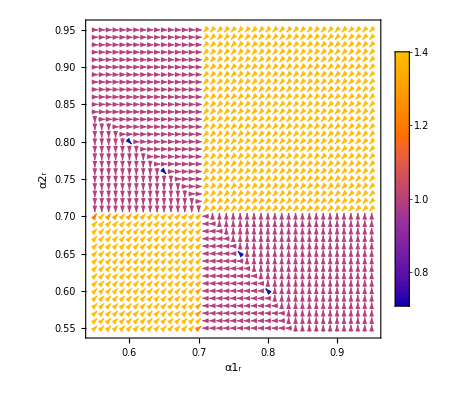

```mathematica
ListVectorPlot[Partition[Partition[Flatten[combined2[[All,{1,2,5,8}]]],2],2], FrameLabel-> {"α1_r","α2_r"}, PlotLegends->Automatic, VectorPoints -> All]
```

```mathematica
(*Export["combined2.mat", combined2]*)
```

I compare these results to a system that test mutant invasion not as a change in average frequency, but in comparing initial frequency to later frequency. The qualitative result is the same, but the plot is different for reasons discussed in the word doc accompanying my email:

```mathematica
CleanFNHricm2[lar1_,har1_,lar2_,har2_,c1_,p_,d1_]:=
(*combineLists[*)
Partition[Flatten[
ParallelTable[{Off[MapThread::mptd];
solution=Reap[NDSolve[ SystemNMH[ar1,ar2, c1,0.5,0.5,1,1,ic1,(1-ic1)],{u1, v1}, {t,0,10000},Method ->Automatic, MaxSteps->20^7,DiscreteVariables->{β,η}]];

sol=solution[[1,1]];
(*Estimate the period of the cycle resident population, and store that period as T1: *)

timesa=Flatten[solution[[2]],1][[All,1]];
(*timesa = minima or maxima of the cycle of host 1*)
values=Flatten[solution[[2]],1][[All,2]];
(*values = freauency of host a reaped at a mimimum or maximum. *)

(*Test to see if the system cycles. If it does not, assign an arbitrary period to it. *)
If[ Length[timesa]<4, times ={1000,1200,1400,1600,1800,2000}, times=timesa ];


TF=2*Median[Differences[Drop[Flatten[times],1]]];


{u1test,v1test}= {u1[10000],v1[10000]}  /.Flatten[sol];

Which[ (*Test 1*) TF==400 &&v1test>0.5, 
(*Simulation for a system without cycling, and a fixed host and symbiont 1: *)
(*Value 1*) {ar1,
ar2,ic1,
(*Initial conditions *)
u1f=If[u1test > 0.5,1,0];
v1f=1;
				   
m11=0.05*v1f;
(*Subtract the frequency of the mutant from the frequency of the resident. *)
v1fm=v1f-m11;

(*************************** A slightly lower ar1: **************************)
am1=ar1-d1;
(*The mutant has a slightly lower ar*)
(*SystemINVH1[α1_,α1m_,α2_,c_,x1_,x1m_,x2_,γ1_,γ1m_,γ2_,u10_,v10_,v1m0_]*)
sol4=NDSolve[SystemINVH1[ar1(*a match*), am1 (*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x1*),0.5(*x1m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u1f(*u10*),v1fm(*u1m0*),m11(*v1final*)], {u1,v1m,v1},{t,0,6*TF},DiscreteVariables->{β,μ,η}, MaxSteps->20^7];
(*Test to see if the mutant invades after invasion by comparing to its initial frequency: *)

{u1ans,m1ans,v1ans}= {u1[t],v1m[t],v1[t]}  /.Flatten[sol4];


avg1b=FindAverage[m1ans, 3*TF,6*TF];

sh2=If[avg1b>m11, 1,0],

(***************A slightly higher version of ar1: ****************)
am2=ar1+d1;

sol5=NDSolve[SystemINVH1[ar1(*a match*), am2 (*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x1*),0.5(*x1m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u1f(*u10*),v1fm(*u1m0*),m11(*v1final*)], {u1,v1m,v1},{t,0,6*TF},DiscreteVariables->{β,μ,η}, MaxSteps->20^7];
(*Test to see if the mutant invades after invasion by comparing to its initial frequency: *)

{u1ans,m1ans,v1ans}= {u1[t],v1m[t],v1[t]}   /.Flatten[sol5];


avg2b=FindAverage[m1ans, 3*TF,6*TF];

sh1=If[avg2b>m11, 1,0],
(sh1-sh2),

0,

0,0
},


 (*Test 3 *)TF==400 &&v1test<0.5,(*Value 2: *)
(*Symbiont 2 fixes and host 2 fixes.  *)


{ar1,
ar2,ic1,
{u2f,v2f}={If[u1test<0.5,1,0],1}  ;
  					   
m21=Abs[0.05*v2f];
(*Subtract the frequency of the mutant from the frequency of the resident. *)
v2fm=Abs[v2f-m21];


(*************************** A slightly lower ar1: **************************)
(*Symbiont 1 is extinct and does not mutate. *)
0,

(***************A slightly higher version of ar1: ****************)

0,
0,
(********************** A slightly lower version of ar2 *********************)

am1=ar2-d1;
(*SystemINVH2[α1_,α2m_,α2_,c_,x1_,x2m_,x2_,γ1_,γ2m_,γ2_,u20_,v2m0_,v20_]*)
sol4=NDSolve[SystemINVH2[ar1(*a match*), am1(*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u2f,m21(*v2m0*),v2fm(*v20*)], {u2,v2m,v2},{t,0,6*TF}, DiscreteVariables->{δ,μ,η},MaxSteps->20^7];

{u2ans,m2ans,v2ans}= {u2[t],v2m[t],v2[t]}  /.Flatten[sol4];



avg1b=FindAverage[m2ans, 3*TF,6*TF];

sl1=If[avg1b>m21, 1,0],

(****************A slightly higher version of ar2 ****************)
am2=ar2+d1;

sol5=NDSolve[SystemINVH2[ar1(*a match*), am2 (*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u2f(*u20*),m21(*v2m0*),v2fm(*v20*)], {u2,v2m,v2},{t,0,6*TF}, DiscreteVariables->{δ,μ,η},MaxSteps->20^7];

{u2ans,m2ans,v2ans}= {u2[t],v2m[t],v2[t]} /.Flatten[sol5];


avg2b=FindAverage[m2ans, 3*TF,6*TF];

sl2=If[avg2b>m21, 1,0],
(sl2-sl1)
},

(*Test 5*)TF ≠ 400,{Table[{(*Value 5*)
(*The system cycles, so we introduce mutants at every p *T of the resident cycle: *)





(**************************** initial conditions ***************************) 
{u1f,v1f}={u1[st],v1[st]}/.Flatten[sol]; 

 u2f=(1-u1f);
v2f=(1-v1f);               
(*Initial frequencies*)		   
m11=0.05*v1f;
m21=0.05*v2f;

v1fm=v1f-m11;
v2fm=v2f-m21;
ar1,
ar2,
ic1,
(************************* A slightly lower ar1: ***************************)
am1=ar1-d1;
(*SystemINVH1[α1_,α1m_,α2_,c_,x1_,x1m_,x2_,γ1_,γ1m_,γ2_,u10_,v10_,v1m0_]*)
sol5=NDSolve[SystemINVH1[ar1(*a match*), am1(*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1f,v1fm(*v1f*),m11(*v1m0*)], {u1,v1m,v1},{t,0,15*TF}, Method -> Automatic, DiscreteVariables->{β,μ,η},MaxSteps->20^7];

{u1ans,m1ans1,v1ans}= {u1[t],v1m[t],v1[t]}  /.Flatten[sol5];



avg1b=FindAverage[m1ans1, 6*TF,12*TF];

s1=If[avg1b>m11, 1,0],

(************** A slightly higher version of ar1 *********************)
am2=ar1+d1;
(*SystemINVH1[α1_,α1m_,α2_,c_,x1_,x1m_,x2_,γ1_,γ1m_,γ2_,u10_,v10_,v1m0_]*)
sol6=NDSolve[SystemINVH1[ar1(*a match*), am2(*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1f,v1fm(*v1f*),m11(*v1m0*)], {u1,v1m,v1},{t,0,15*TF}, Method -> Automatic, DiscreteVariables->{β,μ,η},MaxSteps->20^7];
{u1ans,m1ans2,v1ans}= {u1[t],v1m[t],v1[t]}  /.Flatten[sol6];



avg2b=FindAverage[m1ans2, 6*TF,12*TF];

s2=If[avg2b>m11, 1,0],
(s2-s1),
(************** A slightly lower version of ar2 *********************)
am3=ar2-d1;
(*SystemINVH2[α1_,α2m_,α2_,c_,x1_,x2m_,x2_,γ1_,γ2m_,γ2_,u20_,v2m0_,v20_]*)
sol6=NDSolve[SystemINVH2[ar1(*a match*), am3(*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u2f,m21(*uf0*),v2fm(*v20*)], {u2,v2m,v2},{t,0,15*TF},Method -> Automatic, DiscreteVariables->{δ,μ,η},MaxSteps->20^7];

{u2ans,m2ans1,v2ans}= {u2[t],v2m[t],v2[t]} /.Flatten[sol6];


avg3b=FindAverage[m2ans1, 6*TF,12*TF];

s3=If[avg3b>m21, 1,0],



(****************A slightly higher version of ar2 ****************)
am4=ar2+d1;
(*SystemINVH2[α1_,α2m_,α2_,c_,x1_,x2m_,x2_,γ1_,γ2m_,γ2_,u20_,v2m0_,v20_]*)
sol7=NDSolve[SystemINVH2[ar1(*a match*), am4 (*am match*),ar2(*a2*),(*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u2f,m21(*uf0*),v2fm(*v20*)], {u2,v2m,v2},{t,0,15*TF}, Method -> Automatic, DiscreteVariables->{δ,μ,η},MaxSteps->20^7];

{u2ans,m2ans2,v2ans}= {u2[t],v2m[t],v2[t]} /.Flatten[sol7];


avg4b=FindAverage[m2ans2, 6*TF,12*TF];

s4=If[avg4b>m21, 1,0],

(s4-s3)



},{st,3000+(p*TF),3000+TF,p*TF}]}]},{ar1,lar1,har1,0.01},{ar2,lar2,har2,0.01},{ic1,0.1,0.9,0.16}]],9];
```

```mathematica
newinvasion=CleanFNHricm2[0.6,0.85,0.6,0.85,1/2,0.1,0.005];
```

```mathematica
combinednewinvasion=combineLists[newinvasion];
```

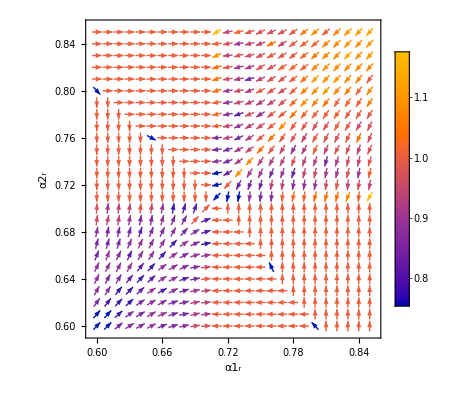

```mathematica
ListVectorPlot[Partition[Partition[Flatten[combinednewinvasion[[All,{1,2,6,9}]]],2],2], FrameLabel-> {"α1_r","α2_r"}, PlotLegends->Automatic, VectorPoints -> All]
```

I wrote a similar simulation for invading symbionts:

```mathematica
(********************** A slightly lower version of ar2 *********************)

SymbiontInvFNric[lar1_,har1_,lar2_,har2_,c1_,p_,d1_,a_]:=
combineLists[
Partition[(*<- Regroup table results*)
Flatten[(*<- Remove internal structure*)
ParallelTable[{Off[MapThread::mptd]; (*<- FindAverage sometimes returns a MapThread error when an interpolating function that lacks a necessary dimension is passed to it. I think occurs when the interpolating function value is constant for an entire sampled region. This is to be expected when a strategist goes extinct so I've turned this error off. *)

(*Run the system of equations, note that I can modulate the shape of the trade-off using the parameter C1, and can vary the initial conditions using the u10 and v10 terms.  *)
solution=Reap[NDSolve[ SystemNMS[ar1,ar2, c1,0.5,0.5,1,1,ic,(1-ic)],{u1, v1}, {t,0,10000},Method ->Automatic, MaxSteps->20^7,DiscreteVariables->{β,η},PrecisionGoal->a, AccuracyGoal-> a]];

sol=solution[[1,1]];
(*Estimate the period of the cycle resident population, and store that period as T1: *)

times=Flatten[solution[[2]],1][[All,1]];
(*timesa = minima or maxima of the cycle of host 1*)
values=Flatten[solution[[2]],1][[All,2]];
(*values = freauency of host a reaped at a mimimum or maximum. *)

(*Test to see if the system cycles. If it does not, assign an arbitrary period to it. *)
If[ Length[times]<4, TF=400, TF=2*Median[Differences[Drop[Flatten[times],1]]] ];

(*If the population fails to cycle we designate an arbitrary period of 400 (which is different from any of the "natural" periods for our parameters). Else, we find the differences between extrema to determine the period.  *)


{utest,v1test}= {u1[9999],v1[9999]}  /.Flatten[sol];

Which[ (*Test 1*) TF==400 &&utest>0.5, 
(*Simulation for a system without cycling, and a fixed host and symbiont 1: *)
(*Value 1*) {ar1,ar2,ic,
(*Initial conditions: *)
{u1f,v1f}={1,If[v1test>0.5,1,0]} ;
(*Because there are some cases where host 2 fixes we also test for this case above.*)				   
m11=Abs[0.05*u1f];
(*Subtract the frequency of the mutant from the frequency of the resident. *)
u1fm=Abs[u1f-m11];

(*************************** A slightly lower ar1: **************************)
am1=ar1-d1;
(*The mutant has a slightly lower ar1*)
sol4=NDSolve[SystemINVS1[ar1(*a match*), am1 (*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x1*),0.5(*x1m*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u1fm(*u10*),m11(*u1m0*),v1f(*v1final*)], {u1,u1m,v1},{t,0,6*TF},DiscreteVariables->{β,μ,η}, MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];
(*Test to see if the mutant invades after invasion by comparing to its initial frequency: *)

{u1ans,m1ans,v1ans}= {u1[t],u1m[t],v1[t]}  /.Flatten[sol4];


avg1b=FindAverage[m1ans, 3*TF,6*TF];
(*Mutants with greater fitness will increase from their intial average frequency. This was a critical change for creating plots that made sense. Word doc from email will explain. *)
sl1=If[avg1b>m21, 1,0],

(***************A slightly higher version of ar1: ****************)
am2=ar1+d1;

sol5=NDSolve[SystemINVS1[ar1(*a match*), am2 (*am match*),ar2(*a2*),(*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1fm(*u10*),m11(*v1f*),v1f(*u1m0*)], {u1,u1m,v1},{t,0,6*TF}, MaxSteps->20^7,DiscreteVariables->{β,μ,η},PrecisionGoal->a, AccuracyGoal-> a];


{u1ans,m1ans,v1ans}= {u1[t],u1m[t],v1[t]}  /.Flatten[sol5];


avg2b=FindAverage[m1ans, 3*TF,6*TF];

sh1=If[avg2b>m21, 1,0],
(sh1-sl1),(*This is the vector for the ar1 component in the final plot. *)

(*ar2 does not evolve because symbiont 2 is extinct. *)
(*************** A slightly lower version of ar2 *********************)
(*Symbiont 2 does not evolve because it is extinct. *)
0,


(****************A slightly higher version of ar2 ****************)
0,
(****************Difference between values ****************)
0(*Vector for the ar2 component. *)
},


 (*Test 2 *)TF==400 &&utest<0.5,(*Value 2: *)
(*Symbiont 2 fixes and host 2 fixes.  *)


{  ar1,ar2,ic,
{u2f,v2f}={1,If[v1test<0.5,1,0]};

(*Mutants invade with a frequency that is proportional to the frequency of the type they invade: *)		   
m21=Abs[0.05*u2f];
(*Subtract the frequency of the mutant from the frequency of the resident. *)
u2fm=Abs[u2f-m21];


(*************************** A slightly lower ar1: **************************)
(*Symbiont 1 is extinct and does not mutate. *)
0,

(***************A slightly higher version of ar1: ****************)

0,
(***************Difference between values ****************)
0,
(********************** A slightly lower version of ar2 *********************)

am1=ar2-d1;

sol4=NDSolve[SystemINVS2[ar1(*a match*), am1(*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u2fm,m21(*uf0*),v2f(*v20*)], {u2,u2m,v2},{t,0,6*TF}, DiscreteVariables->{δ,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];

{u2ans,m2ans,v2ans}= {u2[t],u2m[t],v2[t]}  /.Flatten[sol4];



avg1b=FindAverage[m2ans, 3*TF,6*TF];

sl2=If[avg1b>m21, 1,0],

(****************A slightly higher version of ar2 ****************)
am2=ar2+d1;

sol5=NDSolve[SystemINVS2[ar1(*a match*), am2 (*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u2fm,m21(*uf0*),v2f(*v20*)], {u2,u2m,v2},{t,0,6*TF}, DiscreteVariables->{δ,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];

{u2ans,m2ans,v2ans}= {u2[t],u2m[t],v2[t]} /.Flatten[sol5];


avg2b=FindAverage[m2ans, 3*TF,6*TF];

sh2=If[avg2b>m21, 1,0],
(sh2-sl2)
},

(*Test 3*)TF ≠400,Table[{(*Value 3*)
ar1,ar2,ic,
(************************* initial conditions ***************************) 
{u1f,v1f}={u1[st],v1[st]}/.Flatten[sol]; 

 u2f=(1-u1f);
v2f=(1-v1f);               
(*Initial frequencies*)		   
m11=0.05*u1f;
m21=0.05*u2f;

u1fm=u1f-m11;
u2fm=u2f-m21;

(********************** A slightly lower ar1: ***************************)
am1=ar1-d1;
sol5=NDSolve[SystemINVS1[ar1(*a match*), am1(*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1fm,m11(*uf0*),v1f(*v20*)], {u1,u1m,v1},{t,0,12*TF}, Method -> Automatic, DiscreteVariables->{β,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];

{u1ans,m1ans1,v1ans}= {u1[t],u1m[t],v1[t]}  /.Flatten[sol5];



avg1b=FindAverage[m1ans1, 6*TF,12*TF];

s1=If[avg1b>m11, 1,0],

(************** A slightly higher version of ar1 *********************)
am2=ar1+d1;
sol6=NDSolve[SystemINVS1[ar1(*a match*), am2(*am match*),ar2(*a2*), (*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u1fm,m11(*uf0*),v1f(*v20*)], {u1,u1m,v1},{t,0,12*TF}, Method -> Automatic, DiscreteVariables->{β,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];
{u1ans,m1ans2,v1ans}= {u1[t],u1m[t],v1[t]}  /.Flatten[sol6];



avg2b=FindAverage[m1ans2, 6*TF,12*TF];

s2=If[avg2b>m11, 1,0],
(s2-s1),
(************** A slightly lower version of ar2 *********************)
am3=ar2-d1;

sol6=NDSolve[SystemINVS2[ar1(*a match*), am3(*am match*),ar2(*a2*),(*c: *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),(*values of γ: *)1(*γ*),1(*γm*),1(*γ2*),u2fm,m21(*uf0*),v2f(*v20*)], {u2,u2m,v2},{t,0,12*TF},Method -> Automatic, DiscreteVariables->{δ,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];

{u2ans,m2ans1,v2ans}= {u2[t],u2m[t],v2[t]} /.Flatten[sol6];


avg3b=FindAverage[m2ans1, 6*TF,12*TF];

s3=If[avg3b>m21, 1,0],



(****************A slightly higher version of ar2 ****************)
am4=ar2+d1;

sol7=NDSolve[SystemINVS2[ar1(*a match*), am4 (*am match*),ar2(*a2*),(*c *)c1,0.5 (*x*),0.5(*xm*),0.5(*x2*),1(*γ*),1(*γm*),1(*γ2*),u2fm,m21(*uf0*),v2f(*v20*)], {u2,u2m,v2},{t,0,12*TF}, Method -> Automatic, DiscreteVariables->{δ,μ,η},MaxSteps->20^7,PrecisionGoal->a, AccuracyGoal-> a];

{u2ans,m2ans2,v2ans}= {u2[t],u2m[t],v2[t]} /.Flatten[sol7];


avg4b=FindAverage[m2ans2, 6*TF,12*TF];

s4=If[avg4b>m21, 1,0],
(s4-s3)},{st,3000+(p*TF),3000+TF,p*TF}](*<- closing bracket for table*)
](*<- closing bracket for Which Function*)


},{ar1,lar1,har1,0.01},{ar2,lar2,har2,0.01},{ic,0.1,0.9,0.16}](*<- Closing bracket for Parallel Table*)],9](*<- Closing bracket for Partition*)](*<- Closing bracket for CombineLists*)
```